```mathematica
Quit[];
```

```mathematica
$LoadAddOns = {"FeynArts","FeynHelpers"};
<< FeynCalc`
$FAVerbose = 0;
```

FeynCalc 10.0.0 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.11 (25 Mar 2022) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynHelpers 1.3.0, for more information see the accompanying publication.

Have a look at the supplied examples. If you use FeynHelpers in your research, please cite

• V. Shtabovenko, "FeynHelpers: Connecting FeynCalc to FIRE and Package-X", Comput. Phys. Commun., 218, 48-65, 2017, arXiv:1611.06793

Furthermore, remember to cite the authors of the tools that you are calling from FeynHelpers, which are

• FIRE by A. Smirnov, if you are using the function FIREBurn.

• Package-X by H. Patel, if you are using the function PaXEvaluate.

```mathematica
FAPatch[PatchModelsOnly->True,FAModelsDirectory->FileNameJoin[{NotebookDirectory[],"Simple_Yukawa_FA"}]]
```

Successfully patched FeynArts.

```mathematica
FCClearScalarProducts[];
SP[p,p]=s;
```

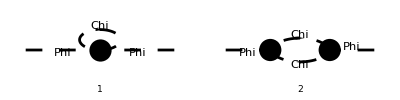

```mathematica
ComplexScalarLoopDiags = InsertFields[CreateTopologies[1, 1 -> 1, ExcludeTopologies->{Tadpoles,WFCorrections}],S[1]->S[1], InsertionLevel->{Particles},ExcludeParticles->{S[1],F[1],F[2]},Model -> FileNameJoin[{NotebookDirectory[],"Simple_Yukawa_FA", "Simple_Yukawa_FA"}], GenericModel -> FileNameJoin[{NotebookDirectory[],"Simple_Yukawa_FA", "Simple_Yukawa_FA"}]];
Paint[ComplexScalarLoopDiags, Numbering->Simple, SheetHeader->None,ColumnsXRows->{4,1},ImageSize->{400,100}];
```

```mathematica
ComplexScalarLoopAmp[0]=Contract/@FCFAConvert[CreateFeynAmp[DiagramExtract[ComplexScalarLoopDiags,2]],IncomingMomenta->{p},OutgoingMomenta->{p},LoopMomenta->{q},ChangeDimension->D,DropSumOver->True,UndoChiralSplittings->True,SMP->True,FinalSubstitutions->M$FACouplings];
```

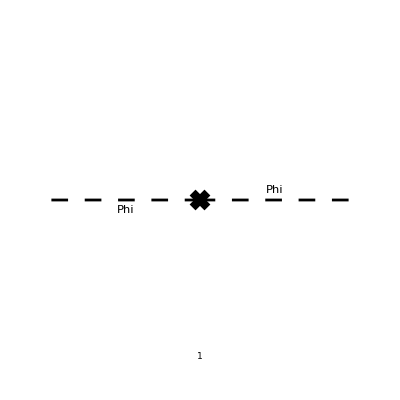

```mathematica
CTDiags = InsertFields[CreateCTTopologies[1, 1 -> 1,ExcludeTopologies->{Tadpoles,WFCorrectionCTs}],S[1]->S[1], InsertionLevel->{Particles}, Model -> FileNameJoin[{NotebookDirectory[],"Simple_Yukawa_FA", "Simple_Yukawa_FA"}], GenericModel -> FileNameJoin[{NotebookDirectory[],"Simple_Yukawa_FA", "Simple_Yukawa_FA"}]];
Paint[CTDiags, Numbering->Simple, SheetHeader->None,ColumnsXRows->{2,1},ImageSize->{200,100}];
AmpCT[0]=Contract/@FCFAConvert[CreateFeynAmp[CTDiags,Truncated->True],IncomingMomenta->{p},OutgoingMomenta->{p},ChangeDimension->D,DropSumOver->True,UndoChiralSplittings->True,SMP->True,FinalSubstitutions->M$FACouplings];
```

```mathematica
Const1[x_]:=1;
Const0[x_]:=0;
evalLoop[ex_]:=ex//TID[#,q,ToPaVe->True]&//DotSimplify[#,Expanding->False]&//DiracSimplify[#,DiracSubstitute67->True]&//Collect2[#,{A0,B0,C0,D0}]&;
processLoop[exs_]:=(
a1=FCTraceFactor/@DotSimplify[#,Expanding->False]&/@exs;
a2=evalLoop/@a1;
a3=Total[a2];
a4=ChangeDimension[PaXEvaluate[a3],4]//Expand
)
```

```mathematica
ComplexScalarLoopAmp[1]=ComplexScalarLoopAmp[0]//processLoop;
ComplexScalarLoopAmp[2]=(ComplexScalarLoopAmp[1]+Total[AmpCT[0]])//Expand;
```

Get::noopen: Cannot open C:\Users\hypercube256\AppData\Roaming\Mathematica\Applications\X\PacletInfo.m.

Part::partd: Part specification $Failed⟦2⟧ is longer than depth of object.

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[2,FeynCalc`PackageX`Private`n1__~~.~~FeynCalc`PackageX`Private`n2__~~.~~FeynCalc`PackageX`Private`n3__:>{FeynCalc`PackageX`Private`n1,FeynCalc`PackageX`Private`n2,FeynCalc`PackageX`Private`n3}].

Identity::argx: Identity called with 2 arguments; 1 argument is expected.

ToExpression::notstrbox: FeynCalc`PackageX`Private`n1__~~.~~FeynCalc`PackageX`Private`n2__~~.~~FeynCalc`PackageX`Private`n3__:>{FeynCalc`PackageX`Private`n1,FeynCalc`PackageX`Private`n2,FeynCalc`PackageX`Private`n3} is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Identity::argx: Identity called with 2 arguments; 1 argument is expected.

```mathematica
RNCond1=Simplify[ComplexScalarLoopAmp[2]/.{s->mPhi^2},Assumptions->mPhi>0]//Re//ComplexExpand//Refine[#,Assumptions->{mPhi>2mChi>0}]&;
RNCond2=Simplify[D[ComplexScalarLoopAmp[2],s]/.{s->mPhi^2},Assumptions->mPhi>0]//Re//ComplexExpand//Refine[#,Assumptions->{mPhi>2mChi>0}]&;
RNRes=Solve[{RNCond1==0,RNCond2==0},{FR$delta({mPhi},{}),FR$deltaZ({Phi,Phi},{{}})}];
```

```mathematica
ComplexScalarLoopAmpLeft=(ComplexScalarLoopAmp[2]/.RNRes[[1]])/.ScaleMu->1//ComplexExpand//Refine[#,Assumptions->{mPhi>2mChi>0,Im[s]>0}]&//FullSimplify;
```

```mathematica
ComplexScalarLeft[s1_,m_,coup_]:=ComplexScalarLoopAmpLeft/.{s->s1,mPhi->1,mChi->m,tau1->4π m √coup};
```

```mathematica
RNCond1=Simplify[ComplexScalarLoopAmp[2]/.{s->mPhi^2},Assumptions->mPhi>0]//Re//ComplexExpand//Refine[#,Assumptions->{2mChi>mPhi>0}]&;
RNCond2=Simplify[D[ComplexScalarLoopAmp[2],s]/.{s->mPhi^2},Assumptions->mPhi>0]//Re//ComplexExpand//Refine[#,Assumptions->{2mChi>mPhi>0}]&;
RNRes=Solve[{RNCond1==0,RNCond2==0},{FR$delta({mPhi},{}),FR$deltaZ({Phi,Phi},{{}})}];
```

```mathematica
ComplexScalarLoopAmpRight=(ComplexScalarLoopAmp[2]/.RNRes[[1]])/.ScaleMu->1//ComplexExpand//Refine[#,Assumptions->{2mChi>mPhi>0,Im[s]>0}]&//FullSimplify;
```

```mathematica
ComplexScalarRight[s1_,m_,coup_]:=ComplexScalarLoopAmpRight/.{s->s1,mPhi->1,mChi->m,tau1->4π m √coup};
```

```mathematica
ComplexScalarAmp[s_,m_,coup_]=If[m>1/2,ComplexScalarRight[s,m,coup],ComplexScalarLeft[s,m,coup]];
```

```mathematica
ComplexScalarLeft[s,m,c]
ComplexScalarRight[s,m,c]
```

1/2 c m^2 (1/s(s^2 (s-4 m^2)^2)^(1/4) ⅇ^(1/2 ⅈ arg(s (s-4 m^2))) (log(ⅇ^(-1/2 ⅈ arg(s (s-4 m^2))) ((s^2 (s-4 m^2)^2)^(1/4)+(2 m^2-s) ⅇ^(1/2 ⅈ arg(s (s-4 m^2)))) ((s^2 (s-4 m^2)^2)^(1/4) ⅇ^(1/2 ⅈ arg(s (s-4 m^2)))+2 m^2-s))+2 ⅈ arg(√(s (s-4 m^2))+2 m^2-s)+2 log(1/m^2)-log(4))-(4 m^2 s log((1-√(1-4 m^2))/(2 m^2)-1))/(√(1-4 m^2))+2 (((6 m^2-1) log((1-√(1-4 m^2))/(2 m^2)-1))/(√(1-4 m^2))+s-1))

1/2 c m^2 (1/s(s^2 (s-4 m^2)^2)^(1/4) ⅇ^(1/2 ⅈ arg(s (s-4 m^2))) (log(ⅇ^(-1/2 ⅈ arg(s (s-4 m^2))) ((s^2 (s-4 m^2)^2)^(1/4)+(2 m^2-s) ⅇ^(1/2 ⅈ arg(s (s-4 m^2)))) ((s^2 (s-4 m^2)^2)^(1/4) ⅇ^(1/2 ⅈ arg(s (s-4 m^2)))+2 m^2-s))+2 ⅈ arg(√(s (s-4 m^2))+2 m^2-s)+2 log(1/m^2)-log(4))-(2 arg(1+(ⅈ (√(4 m^2-1)+ⅈ))/(2 m^2)) (2 m^2 (s-3)+1))/(√(4 m^2-1))+2 s-2)

```mathematica
SpinorLoopDiags = InsertFields[CreateTopologies[1, 1 -> 1, ExcludeTopologies->{Tadpoles,WFCorrections}],S[1]->S[1], InsertionLevel->{Particles},ExcludeParticles->{S[1],S[2],F[2]},Model -> FileNameJoin[{NotebookDirectory[],"Simple_Yukawa_FA", "Simple_Yukawa_FA"}], GenericModel -> FileNameJoin[{NotebookDirectory[],"Simple_Yukawa_FA", "Simple_Yukawa_FA"}]];
Paint[FermionLoopDiags, Numbering->Simple, SheetHeader->None,ColumnsXRows->{4,1},ImageSize->{400,100}];
```

```mathematica
SpinorLoopAmp[0]=Contract/@FCFAConvert[CreateFeynAmp[SpinorLoopDiags],IncomingMomenta->{p},OutgoingMomenta->{p},LoopMomenta->{q},ChangeDimension->D,DropSumOver->True,UndoChiralSplittings->True,SMP->True,FinalSubstitutions->M$FACouplings];
```

```mathematica
SpinorLoopAmp[1]=SpinorLoopAmp[0]//processLoop;
SpinorLoopAmp[2]=(SpinorLoopAmp[1]+Total[AmpCT[0]])//Expand;
```

Get::noopen: Cannot open C:\Users\hypercube256\AppData\Roaming\Mathematica\Applications\X\PacletInfo.m.

Part::partd: Part specification $Failed⟦2⟧ is longer than depth of object.

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[2,FeynCalc`PackageX`Private`n1__~~.~~FeynCalc`PackageX`Private`n2__~~.~~FeynCalc`PackageX`Private`n3__:>{FeynCalc`PackageX`Private`n1,FeynCalc`PackageX`Private`n2,FeynCalc`PackageX`Private`n3}].

Identity::argx: Identity called with 2 arguments; 1 argument is expected.

ToExpression::notstrbox: FeynCalc`PackageX`Private`n1__~~.~~FeynCalc`PackageX`Private`n2__~~.~~FeynCalc`PackageX`Private`n3__:>{FeynCalc`PackageX`Private`n1,FeynCalc`PackageX`Private`n2,FeynCalc`PackageX`Private`n3} is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Identity::argx: Identity called with 2 arguments; 1 argument is expected.

```mathematica
RNCond1=Simplify[SpinorLoopAmp[2]/.{s->mPhi^2},Assumptions->mPhi>0]//Re//ComplexExpand//Refine[#,Assumptions->{mPhi>2mPsi1>0}]&;
RNCond2=Simplify[D[SpinorLoopAmp[2],s]/.{s->mPhi^2},Assumptions->mPhi>0]//Re//ComplexExpand//Refine[#,Assumptions->{mPhi>2mPsi1>0}]&;
RNRes=Solve[{RNCond1==0,RNCond2==0},{FR$delta({mPhi},{}),FR$deltaZ({Phi,Phi},{{}})}];
```

```mathematica
SpinorLoopAmpLeft=(SpinorLoopAmp[2]/.RNRes[[1]])/.ScaleMu->1//ComplexExpand//Refine[#,Assumptions->{mPhi>2mPsi1>0,Im[s]>0}]&//FullSimplify;
```

```mathematica
SpinorLeft[s1_,m_,coup_]:=SpinorLoopAmpLeft/.{s->s1,mPhi->1,mPsi1->m,Y1->4π √coup};
```

```mathematica
RNCond1=Simplify[SpinorLoopAmp[2]/.{s->mPhi^2},Assumptions->mPhi>0]//Re//ComplexExpand//Refine[#,Assumptions->{2mPsi1>mPhi>0}]&;
RNCond2=Simplify[D[SpinorLoopAmp[2],s]/.{s->mPhi^2},Assumptions->mPhi>0]//Re//ComplexExpand//Refine[#,Assumptions->{2mPsi1>mPhi>0}]&;
RNRes=Solve[{RNCond1==0,RNCond2==0},{FR$delta({mPhi},{}),FR$deltaZ({Phi,Phi},{{}})}];
```

```mathematica
SpinorLoopAmpRight=(SpinorLoopAmp[2]/.RNRes[[1]])/.ScaleMu->1//ComplexExpand//Refine[#,Assumptions->{2mPsi1>mPhi>0,Im[s]>0}]&//FullSimplify;
```

```mathematica
SpinorRight[s1_,m_,coup_]:=SpinorLoopAmpRight/.{s->s1,mPhi->1,mPsi1->m,Y1->4π √coup};
```

```mathematica
SpinorAmp[s_,m_,coup_]=If[m>1/2,SpinorRight[s,m,coup],SpinorLeft[s,m,coup]];
```

```mathematica
TotalAmp[s_]:=ComplexScalarAmp[s,0.3,0.1]+ComplexScalarAmp[s,0.4,0.1]+ComplexScalarAmp[s,0.49,0.1]+ComplexScalarAmp[s,0.6,0.1]+ComplexScalarAmp[s,0.43,0.1]+ComplexScalarAmp[s,0.44,0.1];
```

```mathematica
TotalAmp1[s_]:=ComplexScalarAmp[s,0.47,0.4];
TotalAmp2[s_]:=ComplexScalarAmp[s,0.53,0.4];
```

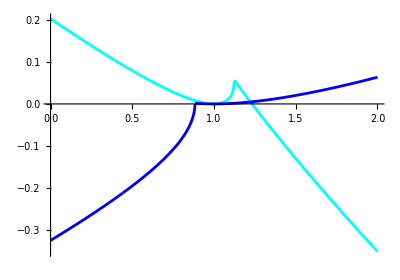

```mathematica
Show[Plot[Re[TotalAmp2[s]],{s,-0,2},PlotRange->Full,MaxRecursion->10,PlotStyle->{Cyan}],Plot[Re[TotalAmp1[s]],{s,-0,2},PlotRange->Full,MaxRecursion->10,PlotStyle->{Blue}],AspectRatio->0.7]
```

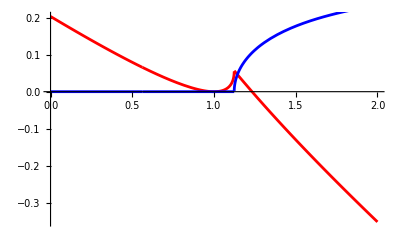

```mathematica
Show[Plot[Re[TotalAmp2[s]],{s,-0,2},PlotRange->Full,MaxRecursion->10,PlotStyle->{Red}],Plot[Im[TotalAmp2[s]],{s,-0,2},PlotRange->Full,MaxRecursion->10,PlotStyle->{Blue}]]
```

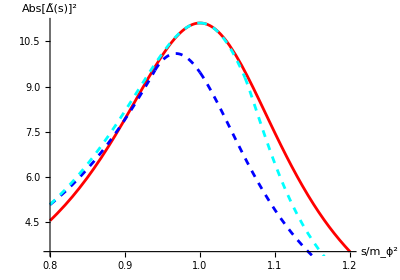

```mathematica
Show[ParametricPlot[{Sqrt[s],Abs[s-1+0.3ⅈ]^-2},{s,0.64,1.44},PlotRange->Full,MaxRecursion->10,AxesLabel->{s/Subscript[m, ϕ]^2,Abs[OverTilde[Δ][s]]^2},PlotStyle->{Red}],ParametricPlot[{Sqrt[s],Abs[s-1+0.3ⅈ+TotalAmp1[s]]^-2},{s,0.64,1.44},PlotRange->Full,MaxRecursion->10,AxesLabel->{s/Subscript[m, ϕ]^2,Abs[OverTilde[Δ][s]]^2},PlotStyle->{Dashed, Blue}],ParametricPlot[{Sqrt[s],Abs[s-1+0.3ⅈ+TotalAmp2[s]]^-2},{s,0.64,1.44},PlotRange->Full,MaxRecursion->10,AxesLabel->{s/Subscript[m, ϕ]^2,Abs[OverTilde[Δ][s]]^2},PlotStyle->{Dashed, Cyan}],AspectRatio->0.7]
```

```mathematica
ComplexScalarContAmp[s_?NumericQ]:=NIntegrate[ComplexScalarLeft[s,m,1]ComplexScalarSpectrum[m],{m,0,1/2},MaxRecursion->20]+NIntegrate[ComplexScalarRight[s,m,1]ComplexScalarSpectrum[m],{m,1/2,2},MaxRecursion->20];
SpinorContAmp[s_?NumericQ]:=NIntegrate[SpinorLeft[s,m,1]SpinorSpectrum[m],{m,0,1/2},MaxRecursion->20]+NIntegrate[SpinorRight[s,m,1]SpinorSpectrum[m],{m,1/2,2},MaxRecursion->20];
```

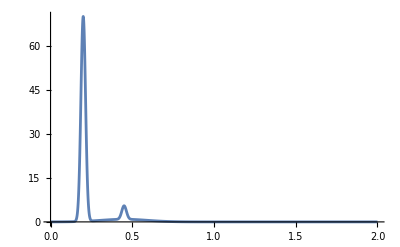

```mathematica
ComplexScalarSpectrum[m_]:=70 Exp[-((m-0.2)/0.02)^2]+0.9 Exp[-((m-0.45)/0.2)^2]+4.6 Exp[-((m-0.45)/0.02)^2];
Plot[ComplexScalarSpectrum[m],{m,0,2},PlotRange->Full]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 20 recursive bisections in m near {m} = {0.674633}. NIntegrate obtained 0.429712+0. ⅈ and 6.85624×10^-7 for the integral and error estimates.

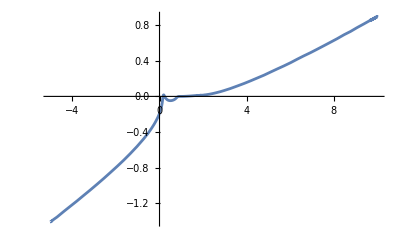

```mathematica
Plot[Re[ComplexScalarContAmp[s]],{s,-5,10},PlotRange->Full]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 20 recursive bisections in m near {m} = {0.674633}. NIntegrate obtained 0.429712+0. ⅈ and 6.85624×10^-7 for the integral and error estimates.

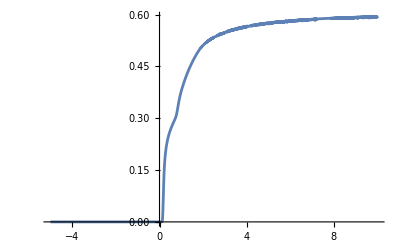

```mathematica
Plot[Im[ComplexScalarContAmp[s]],{s,-5,10},PlotRange->Full]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1.13074×10^-20+1.18636×10^-19 ⅈ and 3.63604×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

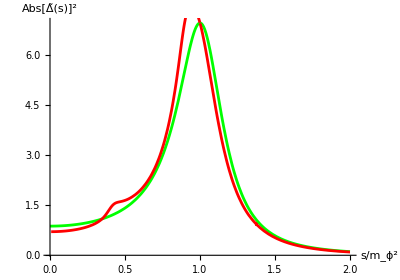

```mathematica
Γ=Im[ComplexScalarContAmp[1]];
Show[ParametricPlot[{Sqrt[s],Abs[s-1+ⅈ Γ]^-2},{s,0,4},PlotRange->Full,MaxRecursion->10,AxesLabel->{s/Subscript[m, ϕ]^2,Abs[OverTilde[Δ][s]]^2},PlotStyle->{Green}],ParametricPlot[{Sqrt[s],Abs[s-1+ComplexScalarContAmp[s]]^-2},{s,0,4},PlotRange->Full,AxesLabel->{s/Subscript[m, ϕ]^2,Abs[OverTilde[Δ][s]]^2},PlotStyle->{Red}],AspectRatio->0.7]
```

```mathematica
HiggsBottom[s1_]:= SpinorLoopAmpLeft/.{s->s1,mPhi->125.11,mPsi1->4.18,Y1->0.017};
3 Im[HiggsBottom[(125.11)^2]]/125.11
```

0.00428702

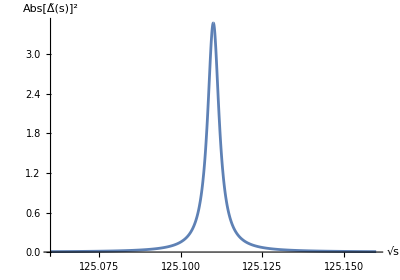

```mathematica
Show[ParametricPlot[{Sqrt[s],Abs[s-125.11^2+3 HiggsBottom[s]]^-2},{s,125.06^2,125.16^2},PlotRange->Full,MaxRecursion->10,AxesLabel->{√s,Abs[OverTilde[Δ][s]]^2}],AspectRatio->0.7]
```

```mathematica
3/(16π)(2×4.18^2)/246^2×125.11×(1-4/896)^(3/2)
```

0.00428293